# Mathematica Tutorial 2

## Sums, Series, Special Functions, and Solving Equations

Jason Ho

## Series

```mathematica
?Series
```

RowBox[{"Series", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], ",", StyleBox["n", "TI"]}], "}"}]}], "]"}] generates a power series expansion for StyleBox["f", "TI"] about the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}] to order SuperscriptBox[RowBox[{"(", RowBox[{StyleBox["x", "TI"], "-", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], ")"}], StyleBox["n", "TI"]]. 
RowBox[{"Series", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["x", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] successively finds series expansions with respect to StyleBox["x", "TI"], then StyleBox["y", "TI"], etc.

A few notes about Series: 
If you want to terminate a series and not worry about the higher order piece, use our previously discussed Postfix (//) command and the Normal command to remove it.

```mathematica
Series[Cos[x],{x,0,5}]
Series[Cos[x],{x,0,5}]//Normal
```

1-x^2/2+x^4/24+O[x]^6

1-x^2/2+x^4/24

Note that if you try and Plot a Series without using Normal, you’ll run into issues. We also recall that, as with when we were plotting derivatives, we have to be mindful of the order in which Mathematica evaluates commands. Pay attention to the command structure below.

General::ivar: 0.000128356 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

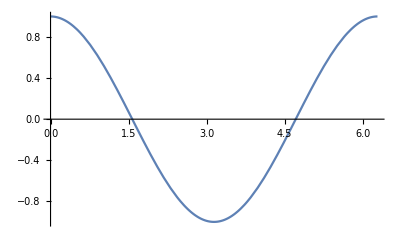

```mathematica
Plot[{Cos[x],Series[Cos[x],{x,0,4}]},{x,0,2π}]
```

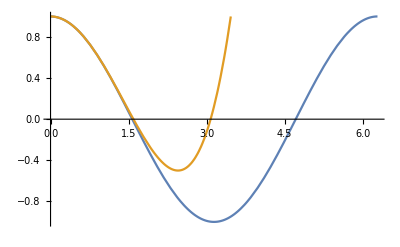

```mathematica
Plot[{Cos[x],Evaluate[Series[Cos[x],{x,0,4}]//Normal]},{x,0,2π},PlotRange->{-1,1}]
```

You can expand about any value you’d like; you can even use Mathematica to look at the asymptotic behaviour of a function (i.e. expand out at ∞). Recall that, as when we

25/288-EulerGamma/24+1/(24 (4+x))+((415-300 EulerGamma+72 EulerGamma^2+12 π^2) (4+x))/3456+1/41472(4+x)^2 (5845-4980 EulerGamma+1800 EulerGamma^2-288 EulerGamma^3+300 π^2-144 EulerGamma π^2+288 PolyGamma[2,1])+1/2488320(4+x)^3 (380555-350700 EulerGamma+149400 EulerGamma^2-36000 EulerGamma^3+4320 EulerGamma^4+24900 π^2-18000 EulerGamma π^2+4320 EulerGamma^2 π^2+648 π^4+36000 PolyGamma[2,1]-17280 EulerGamma PolyGamma[2,1])

ⅇ^(x (-1-Log[1/x])) √(2 π) √(1/x)

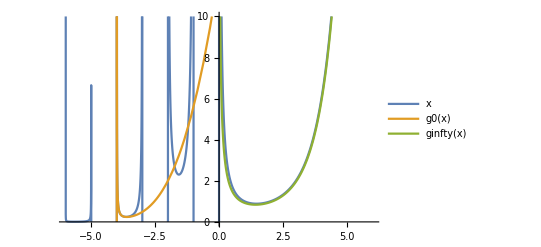

```mathematica
g0[x_]:=Evaluate[Series[Gamma[x],{x,-4,3}]//Normal]
ginfty[x_]:=Evaluate[Series[Gamma[x],{x,Infinity,1}]//Normal]
g0[x]
ginfty[x]
Plot[{Gamma[x],g0[x],ginfty[x]},{x,-6,6},PlotRange->{0,10},PlotLegends->"Expressions"]
```

## Sums

```mathematica
?Sum
```

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, … .
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f. 
Sum[f,i] gives the indefinite sum ∑_i f.

The Sum command is similar in structure to the series command. We can define them explicitly or symbolically

```mathematica
Sum[j^2,{j,0,10}]
Sum[j^2,{j,0,n}]
```

385

1/6 n (1+n) (1+2 n)

...and also look at infinite series

```mathematica
Sum[1/j^2,{j,1,Infinity}]
```

π^2/6

Mathematica will recognize known sums and simplify them for you

```mathematica
Series[Exp[x],{x,0,3}]
```

1+x+x^2/2+x^3/6+O[x]^4

```mathematica
g[x_,n_]:=Sum[x^j/j!,{j,0,n}]
g[x,3]
g[x,Infinity]
```

1+x+x^2/2+x^3/6

ⅇ^x

## Special Functions - Bessel Functions

By now, you know a few instances where Bessel functions are very useful. Mathematica has a bunch built in, and a few tools to go with them.

```mathematica
?BesselJ
?BesselY
?BesselK
?BesselI
?BesselJZero
?BesselYZero
```

RowBox[{"BesselJ", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["z", "TI"]}], "]"}] gives the Bessel function of the first kind RowBox[{SubscriptBox[StyleBox["J", "TI"], StyleBox["n", "TI"]], "(", StyleBox["z", "TI"], ")"}].

RowBox[{"BesselY", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["z", "TI"]}], "]"}] gives the Bessel function of the second kind RowBox[{SubscriptBox[StyleBox["Y", "TI"], StyleBox["n", "TI"]], "(", StyleBox["z", "TI"], ")"}].

RowBox[{"BesselK", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["z", "TI"]}], "]"}] gives the modified Bessel function of the second kind RowBox[{SubscriptBox[StyleBox["K", "TI"], StyleBox["n", "TI"]], "(", StyleBox["z", "TI"], ")"}].

RowBox[{"BesselI", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["z", "TI"]}], "]"}] gives the modified Bessel function of the first kind RowBox[{SubscriptBox[StyleBox["I", "TI"], StyleBox["n", "TI"]], "(", StyleBox["z", "TI"], ")"}].

RowBox[{"BesselJZero", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"]}], "]"}] represents the StyleBox["k", "TI"]SuperscriptBox["", "th"] zero of the Bessel function RowBox[{SubscriptBox[StyleBox["J", "TI"], StyleBox["n", "TI"]], "(", StyleBox["x", "TI"], ")"}].
RowBox[{"BesselJZero", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "]"}] represents the StyleBox["k", "TI"]SuperscriptBox["", "th"] zero greater than SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]].

RowBox[{"BesselYZero", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"]}], "]"}] represents the StyleBox["k", "TI"]SuperscriptBox["", "th"] zero of the Bessel function of the second kind RowBox[{SubscriptBox[StyleBox["Y", "TI"], StyleBox["n", "TI"]], "(", StyleBox["x", "TI"], ")"}].
RowBox[{"BesselYZero", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "]"}] represents the StyleBox["k", "TI"]SuperscriptBox["", "th"] zero greater than SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]].

It used to be you had to look up the zeros of these functions in large volumes of books. Luckily, we don’t have to.

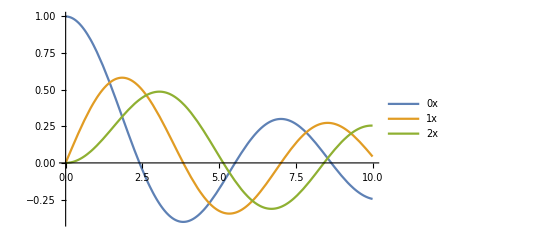

{2.40483,3.83171,5.13562}

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x]},{x,0,10},PlotLegends->"Expressions"]
{N@BesselJZero[0,1],N@BesselJZero[1,1],N@BesselJZero[2,1]}
```

Of course, we could just use some of the techniques we’ve already learned to find these same roots.

```mathematica
FindRoot[BesselJ[0,x],{x,2}]
FindRoot[BesselJ[1,x],{x,4}]
FindRoot[BesselJ[2,x],{x,5}]
```

{x→2.40483}

{x→3.83171}

{x→5.13562}

## Solving Equations

To solve equations (or systems of equations!) in Mathematica, we utilize the Solve[ ] or Reduce[ ] command,

```mathematica
?Solve
```

RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to solve the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"]}], "]"}] solves over the domain StyleBox["dom", "TI"]. Common choices of StyleBox["dom", "TI"] are Reals, Integers, and Complexes.

```mathematica
?Reduce
```

Reduce[expr,vars] reduces the statement expr by solving equations or inequalities for vars and eliminating quantifiers. 
Reduce[expr,vars,dom] does the reduction over the domain dom. Common choices of dom are Reals, Integers, and Complexes.

The differences between the two are subtle, but Reduce is a little more general and will look for relationships and restrictions of parameters when solving systems of equations

```mathematica
Solve[a x-b==0,x]
```

{{x→b/a}}

```mathematica
Reduce[a x-b==0,x]
```

(b==0&&a==0)||(a≠0&&x==b/a)

Not surprisingly, there’s also an NSolve[ ] command if you desire a numerical solution.

```mathematica
?NSolve
```

RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to find numerical approximations to the solutions of the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["Reals", "TI"]}], "]"}] finds solutions over the domain of real numbers.

Also not surprisingly, it works the same as every other numerical command we' ve tackled, so we're not going to dig into it much.

Solve[ ] can only deal with problems that can be solved algebraically.

```mathematica
Solve[Sin[x]==x,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Sin[x]==x,x]

For most realistic cases, we’ll use the FindRoot[ ] command, which deals with input numerically. Whenever we deal with solving numerical equations, wherever possible it’s beneficial to plot your functions first to inspect any problematic regions (asymptotes, multiple solutions, etc)

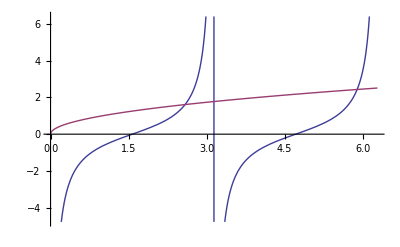

{z→2.58519}

```mathematica
Plot[{-Cot[z],Sqrt[z]},{z,0,2π}]
FindRoot[-Cot[z]==Sqrt[z],{z,π/4}]
```

We can see that we’ve found the first positive solution of this system of equations.